# Surfaces de translation - Quartique de Klein

```mathematica
facteurHomothetie=1/10;
```

```mathematica
(*v0=facteurHomothetie{0.06,0.43};
v2=facteurHomothetie{2.58,4.27};
v4=facteurHomothetie{-0.67,-0.27};
v6=facteurHomothetie{1.69,-0.09};
v8=facteurHomothetie{-0.05, -0.37};
v10=facteurHomothetie{4.69,0.72};
v12=facteurHomothetie{2.83,0.61};*)

(*v0={1-Cos[Pi/18],Sin[2Pi/18]};
v2={{Cos[2Pi/17],-Sin[2Pi/17]},{Sin[2Pi/17],Cos[2Pi/17]}}.v0;
v4={{Cos[2Pi/17],-Sin[2Pi/17]},{Sin[2Pi/17],Cos[2Pi/17]}}.v2;
v6={{Cos[2Pi/17],-Sin[2Pi/17]},{Sin[2Pi/17],Cos[2Pi/17]}}.v4;
v8={{Cos[2Pi/17],-Sin[2Pi/17]},{Sin[2Pi/17],Cos[2Pi/17]}}.v6;
v10={{Cos[2Pi/17],-Sin[2Pi/17]},{Sin[2Pi/17],Cos[2Pi/17]}}.v8;
v12={{Cos[2Pi/17],-Sin[2Pi/17]},{Sin[2Pi/17],Cos[2Pi/17]}}.v10;*)

v0={1.5,2};
v2={-1,1};
v4={-1,1};
v6={-0.3,-1};
v8={1,-0.6};
v10={2,-1};
v12={1.5,1};
ek={v2+v4-v10-v12,v4+v6-v12-v0,v6+v8-v0-v2,v8+v10-v2-v4,v10+v12-v4-v6,v12+v0-v6-v8,v0+v2-v10-v8};
```

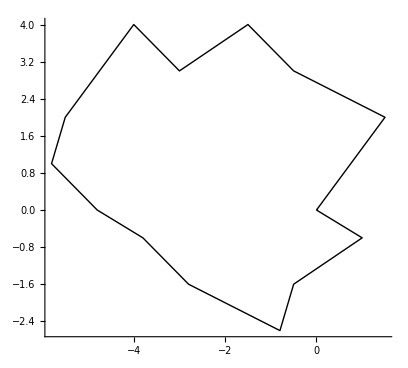

```mathematica
ligneBrisee={{0,0}, v0, v0-v10,v0-v10+v2,v0-v10+v2-v12,v0-v10+v2-v12+v4,-v10+v2-v12+v4,-v10+v2-v12+v4+v6,-v10-v12+v4+v6,-v10-v12+v4+v6+v8,-v10-v12+v6+v8,-v12+v6+v8,-v12+v8,v8,{0,0}};
Graphics[Line[ligneBrisee],Axes->True]
```

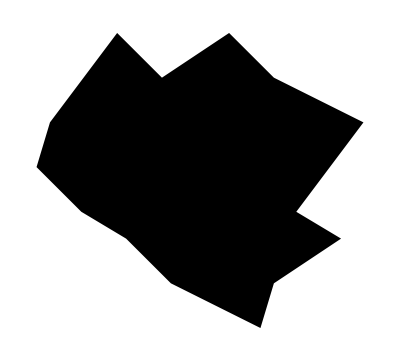

```mathematica
polygone={{0,0}, v0, v0-v10,v0-v10+v2,v0-v10+v2-v12,v0-v10+v2-v12+v4,-v10+v2-v12+v4,-v10+v2-v12+v4+v6,-v10-v12+v4+v6,-v10-v12+v4+v6+v8,-v10-v12+v6+v8,-v12+v6+v8,-v12+v8,v8};
Region[Polygon[polygone]]
```

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
mesh=ToElementMesh[Region[Polygon[polygone]],MeshRefinementFunction->Function[{vertices,area},area>0.004]]
```

ElementMesh[{{-5.8,1.5},{-2.6,4.}},{TriangleElement[<11015>]}]

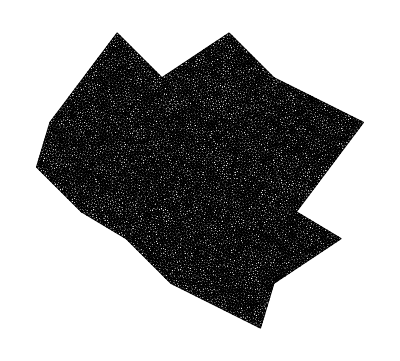

```mathematica
mesh["Wireframe"]
```

```mathematica
m=Table[(ligneBrisee[[i+1]][[2]]-ligneBrisee[[i]][[2]])/(ligneBrisee[[i+1]][[1]]-ligneBrisee[[i]][[1]]),{i,1,14}];
p=Table[ligneBrisee[[i]][[2]]-m[[i]]ligneBrisee[[i]][[1]],{i,1,14}];
```

```mathematica
conditions = {PeriodicBoundaryCondition[u[x,y],If[ligneBrisee[[1]][[1]]<ligneBrisee[[2]][[1]],(x>ligneBrisee[[1]][[1]]&&x<ligneBrisee[[2]][[1]]),(x<ligneBrisee[[1]][[1]]&&x>ligneBrisee[[2]][[1]])]&& y==m[[1]]x+p[[1]],Function[x,x+ek[[1]]]],PeriodicBoundaryCondition[u[x,y],If[ligneBrisee[[3]][[1]]<ligneBrisee[[4]][[1]],(x>ligneBrisee[[3]][[1]]&&x<ligneBrisee[[4]][[1]]),(x<ligneBrisee[[3]][[1]]&&x>ligneBrisee[[4]][[1]])]&& y==m[[3]]x+p[[3]],Function[x,x+ek[[2]]]],PeriodicBoundaryCondition[u[x,y],If[ligneBrisee[[5]][[1]]<ligneBrisee[[6]][[1]],(x>ligneBrisee[[5]][[1]]&&x<ligneBrisee[[6]][[1]]),(x<ligneBrisee[[5]][[1]]&&x>ligneBrisee[[6]][[1]])]&& y==m[[5]]x+p[[5]],Function[x,x+ek[[3]]]],PeriodicBoundaryCondition[u[x,y],If[ligneBrisee[[7]][[1]]<ligneBrisee[[8]][[1]],(x>ligneBrisee[[7]][[1]]&&x<ligneBrisee[[8]][[1]]),(x<ligneBrisee[[7]][[1]]&&x>ligneBrisee[[8]][[1]])]&& y==m[[7]]x+p[[7]],Function[x,x+ek[[4]]]],PeriodicBoundaryCondition[u[x,y],If[ligneBrisee[[9]][[1]]<ligneBrisee[[10]][[1]],(x>ligneBrisee[[9]][[1]]&&x<ligneBrisee[[10]][[1]]),(x<ligneBrisee[[9]][[1]]&&x>ligneBrisee[[10]][[1]])]&& y==m[[9]]x+p[[9]],Function[x,x+ek[[5]]]],PeriodicBoundaryCondition[u[x,y],If[ligneBrisee[[11]][[1]]<ligneBrisee[[12]][[1]],(x>ligneBrisee[[11]][[1]]&&x<ligneBrisee[[12]][[1]]),(x<ligneBrisee[[11]][[1]]&&x>ligneBrisee[[12]][[1]])]&& y==m[[11]]x+p[[11]],Function[x,x+ek[[6]]]],PeriodicBoundaryCondition[u[x,y],If[ligneBrisee[[13]][[1]]<ligneBrisee[[14]][[1]],(x>ligneBrisee[[13]][[1]]&&x<ligneBrisee[[14]][[1]]),(x<ligneBrisee[[13]][[1]]&&x>ligneBrisee[[14]][[1]])]&& y==m[[13]]x+p[[13]],Function[x,x+ek[[7]]]]};
```

```mathematica
valeursMetriquePlate = NDEigensystem[{-Laplacian[u[x,y],{x,y}],conditions[[1]],conditions[[2]],conditions[[3]],conditions[[4]],conditions[[5]],conditions[[6]],conditions[[7]]},u[x,y],{x,y}∈ mesh,10][[1]];
```

```mathematica
ligneBrisee[[3]][[1]]
```

Part::partd: Part specification ligneBrisee⟦3⟧ is longer than depth of object.

ligneBrisee

```mathematica
valeursMetriquePlate*Area[Polygon[polygone]]
```

{5.90856×10^-13,40.5855,43.0877,49.7299,54.5108,65.7058,72.9249,92.5617,111.36,120.337}